```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["ErrorBarPlots`"];
```

## Debye mass HTL Fitting

### Analytic Expression

```mathematica
(* form hep-ph 9703284, vermaseren, larin, Ritbergen *)
ΛQCD=0.2145; 
(* so that for nF=5 we get alpha_s(mz=91.188)=0.1185 (PDG value) 
note that pdg also quotes λqcd=0.214 for nf=5 everything seems consistent*)

(*QCD*)
Nc=3.;CA=Nc; nF=3;
CF=(Nc^2-1)/(2 Nc);
(*coeft of the renormalization group equations*)
β0[Nf_]=(-11Nc+2Nf)/12;
β1[Nf_]=(-68 Nc^2+20Nc Nf+12CF Nf)/(3 32);
β2[Nf_]=-(2857-5033/9 Nf+325/27 Nf^2)/128; (*for Nc=3 only*)
β3[Nf_]=-1/256((149753/6+3564 Zeta[3])-(1078361/162+6508/27 Zeta[3])Nf+(50065/162+6472/81 Zeta[3])Nf^2+1093/729 Nf^3);(*for Nc=3 only*)

γ0[Nf_]=3/4 CF;
γ1[Nf_]=1/16(202/3-20/9 Nf);(*for Nc=3 only*)
γ2[Nf_]=1/64(1249+(-2216/27-160/3 Zeta[3])Nf-140/81 Nf^2);(*for Nc=3 only*)
γ3[Nf_]=1/256(4603055/162+135680/27 Zeta[3]-8800Zeta[5]+(-91723/27-34192/9 Zeta[3]+880 Zeta[4]+18400/9 Zeta[5])Nf+(5242/243+800/9 Zeta[3]-160/3 Zeta[4])Nf^2+(-332/243+64/27 Zeta[3])Nf^3);

b0[Nf_]=-(8β0[Nf])/(2(4π)^2);
b1[Nf_]=-(32 β1[Nf])/(2(4π)^2);

(* Initial conditions of the RG equations, μ in units of Λ_MSbar *)

(*gf[μ_]=1/√(2 b0 Log[μ]+b1 Log[2 Log[μ]]/b0);*)
gf[t_]=1/(√(b0[Nf] t+b1[Nf] Log[t]/b0[Nf]));
asf[t_,Nf_]=-1/(β0[Nf] t)-(β1[Nf] Log[t])/(β0[Nf]^3 t^2)-(β1[Nf]^2(Log[t]^2-Log[t]-1)+β2[Nf] β0[Nf])/(β0[Nf]^5 t^3)+1/(β0[Nf]^7 t^4)( β1[Nf]^3(-Log[t]^3+5/2 Log[t]^2+2Log[t]-1/2)-3 β1[Nf] β2[Nf] β0[Nf] Log[t]+1/2 β3[Nf] β0[Nf]^2);
μ0=2;
t0=Log[μ0^2];
tf=10000 t0;
(*solution of the RG equation to 3 loop*)
mcharm=1.275;(*m(m) in msbar*)
mbottom=4.18;
nf[t_]=If[t<Log[mcharm^2/ΛQCD^2],3,If[t<Log[mbottom^2/ΛQCD^2],4,5]];
sg4=NDSolve[{D[as[t],t]==+β0[nf[t]] as[t]^2+β1[nf[t]] as[t]^3+ β2[nf[t]] as[t]^4+ β3[nf[t]] as[t]^5,as[tf]==asf[tf,nf[tf]]},as,{t,t0,tf},AccuracyGoal->14,WorkingPrecision->32,MaxSteps->10000000];

a4t[t_]= Part[Evaluate[as[t]/.sg4],1];
g4[μ_]=2 π √Part[Evaluate[as[Log[μ^2/ΛQCD^2]]/.sg4],1]; 

mDcal[μ_,T_,c_,d_]:=Re[Sqrt[Nc/3+nF/6]g4[μ T]T+1/(4π)Nc g4[μ T]^2 T Log[Sqrt[Nc/3+nF/6]/g4[μ T]]+c g4[μ T]^2 T+d g4[μ T]^3 T ];
mDcalT[μ_,T_,c_,d_]:=1/T mDcal[μ,T,c,d];
```

NDSolve::precw: The precision of the differential equation ({{as'[t]==1/12 as[t]^2 (-33.+2 If[«3»])+1/96 as[t]^3 (-612.+76. If[«3»])+1/128 as[t]^4 (-2857+5033/9 If[«3»]-325/27 Power[«2»])+1/256 as[t]^5 (-149753/6-1093/729 Power[«2»]-3564 Zeta[«1»]-Power[«2»] Plus[«2»]+If[«3»] Plus[«2»]),as[10000 Log[4]]==0.0000376185},{},{},{},{}}) is less than WorkingPrecision (32.).

NDSolve::ndsz: At t == 2.05914, step size is effectively zero; singularity or stiff system suspected.

### Fitting

```mathematica
β={6.8,6.9,7,7.125,7.25,7.3,7.48};
T={0.1478,0.1642,0.1818,0.2054,0.2317,0.2425,0.2861};
Tclatt=0.1725;
Tccont={0.155,9};
```

```mathematica
md={{0.01285788533869477,0.027132315137228885},{0.12028928865080628,0.053873564496655146},{0.19037780099816687,0.059166795334990474},{0.3109120452477387,0.1316818297643033},{0.48199114786289143,0.053005028839144264},{0.49593688544196995,0.11112511089666832},{0.650670382323598,0.09746020712923346}};
```

```mathematica
σ={0.2251895601811595,0.22626306753517622,0.22732210969450667,0.22836715240557703,0.22939866141481324,0.23041710246864133,0.23142294131348745,0.23241664369577758,0.2333986753619378,0.23436950205839413,0.23532958953157262,0.2362815228929988,0.2372268592775758,0.23816235544215192,0.2390877977204241,0.24000297244608948,0.24090766595284518,0.24180166457438818,0.24268475464441558,0.24354825726371032,0.24439342747245596,0.24522874644059045,0.24605537750976753,0.24687448402164097,0.24768722931786452,0.2484947767400919,0.24929828962997697,0.2500989313291733,0.2509042291387489,0.2517067388416378,0.25250343433127753,0.2532936350821978,0.25407666056892825,0.25485183026599856};
σerr={0.030081446439038928,0.029359609987482882,0.028647500069018894,0.027944803511365135,0.027251207142239997,0.026566397789361706,0.025890062280448545,0.025221887443218793,0.02456156010539068,0.023908767094682593,0.023263195238812706,0.022623106284453298,0.02198745319943568,0.02135841677098904,0.020736140670347125,0.02012076856874362,0.019512444137412266,0.018911311047586643,0.018317512970500494,0.01773688567969639,0.01716858527433901,0.01660690893591471,0.01605107442254311,0.015500299492343661,0.014953801903435926,0.014410799413939468,0.013870509781973794,0.013332150765658468,0.012790660936888465,0.012251045857303633,0.011715340309446487,0.011184001885050032,0.010657488175847607,0.010136256773572327};
```

```mathematica
αcont={0.5138562580709736,0.0027118637679895965};
σcont={0.16949622818854412,0.0009172672238755708};
ccont={-0.15942304870711493,0.0023023051670536016};
```

```mathematica
mDfit=NonlinearModelFit[Table[{T[[n]](155/172.5),md[[n,1]]/T[[n]] √(σcont[[1]]/σ[[n]])},{n,1,Length[T]}],mDcalT[2π,x,d,e],{d,e},x];
{k1,k2}={d,e}/.mDfit["BestFitParameters"];
mDfit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
d | 0.66797 | 0.0979725 | 6.81793 | 0.00103469
e | -0.337732 | 0.0399517 | -8.45353 | 0.000380285

```mathematica
mDfitupper=NonlinearModelFit[Table[{T[[n]](155/172.5),(md[[n,1]]+md[[n,2]])/T[[n]] √(σcont[[1]]/σ[[n]])},{n,1,Length[T]}],mDcalT[2π,x,d,e],{d,e},x];
{k1u,k2u}={d,e}/.mDfitupper["BestFitParameters"];
mDfitupper["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
d | 0.926458 | 0.0843942 | 10.9777 | 0.000109114
e | -0.422495 | 0.0344146 | -12.2766 | 0.0000634635

```mathematica
mDfitlower=NonlinearModelFit[Table[{T[[n]](155/172.5),(md[[n,1]]-md[[n,2]])/T[[n]] √(σcont[[1]]/σ[[n]])},{n,1,Length[T]}],mDcalT[2π,x,d,e],{d,e},x];
{k1l,k2l}={d,e}/.mDfitlower["BestFitParameters"];
mDfitlower["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
d | 0.409481 | 0.166701 | 2.45638 | 0.0574837
e | -0.25297 | 0.0679781 | -3.72134 | 0.013693

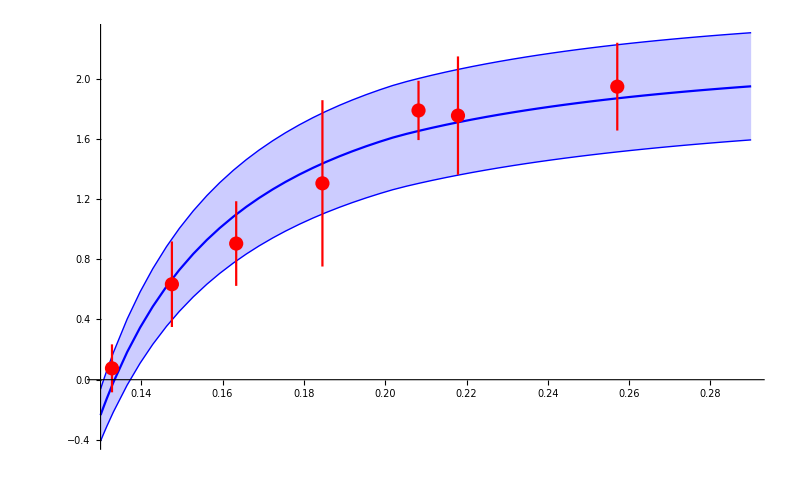

```mathematica
Show[{Plot[{mDcalT[2π,x,k1,k2],mDcalT[2π,x,k1u,k2u],mDcalT[2π,x,k1l,k2l]},{x,0.13,0.29},PlotRange->All,Filling->{1->{2},1->{3}},FillingStyle->Opacity[0.2,Blue],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin}}],ErrorListPlot[Table[{T[[n]](155/172.5),md[[n,1]]/T[[n]] √(σcont[[1]]/σ[[n]]),md[[n,2]]/T[[n]] √(σcont[[1]]/σ[[n]])},{n,1,Length[β]}],PlotRange->All,PlotStyle->{Red}]}]
```

```mathematica
mdrandu[n_]:=Module[{m},m=md[[n,1]]+Abs[RandomVariate[NormalDistribution[0,md[[n,2]]]]];If[m>0,m,0]]
mdrandl[n_]:=Module[{m},m=md[[n,1]]-Abs[RandomVariate[NormalDistribution[0,md[[n,2]]]]];If[m>0,m,0]]
σrand[n_]:=RandomVariate[NormalDistribution[σ[[n]],σerr[[n]]]];
σcontrand:=RandomVariate[NormalDistribution[σcont[[1]],σcont[[2]]]];
```

```mathematica
fitsu={{},{}};
fitsl={{},{}};
SetSharedVariable[fitsu,fitsl];
Module[{k1u,k2u,k1l,k2l},ParallelDo[Quiet[{k1u,k2u}={d,e}/.NonlinearModelFit[Table[{T[[n]](155/172.5),mdrandu[n]/T[[n]] √(σcont[[1]]/σ[[n]])},{n,1,Length[T]}],mDcalT[2π,x,d,e],{d,e},x]["BestFitParameters"];
{k1l,k2l}={d,e}/.NonlinearModelFit[Table[{T[[n]](155/172.5),mdrandl[n]/T[[n]] √(σcont[[1]]/σ[[n]])},{n,1,Length[T]}],mDcalT[2π,x,d,e],{d,e},x]["BestFitParameters"]];
fitsu[[1]]=Append[fitsu[[1]],k1u];
fitsu[[2]]=Append[fitsu[[2]],k2u];
fitsl[[1]]=Append[fitsl[[1]],k1l];fitsl[[2]]=Append[fitsl[[2]],k2l],{i,1,10000}]]
```

```mathematica
kfinalu={Mean[fitsu[[1]]],Mean[fitsu[[2]]]}
kfinall={Mean[fitsl[[1]]],Mean[fitsl[[2]]]}
```

```mathematica
k1final={Mean[fits[[1]]],StandardDeviation[fits[[1]]]}
k2final={Mean[fits[[2]]],StandardDeviation[fits[[2]]]}
```

{0.653859,0.19456}

{-0.331389,0.0747726}

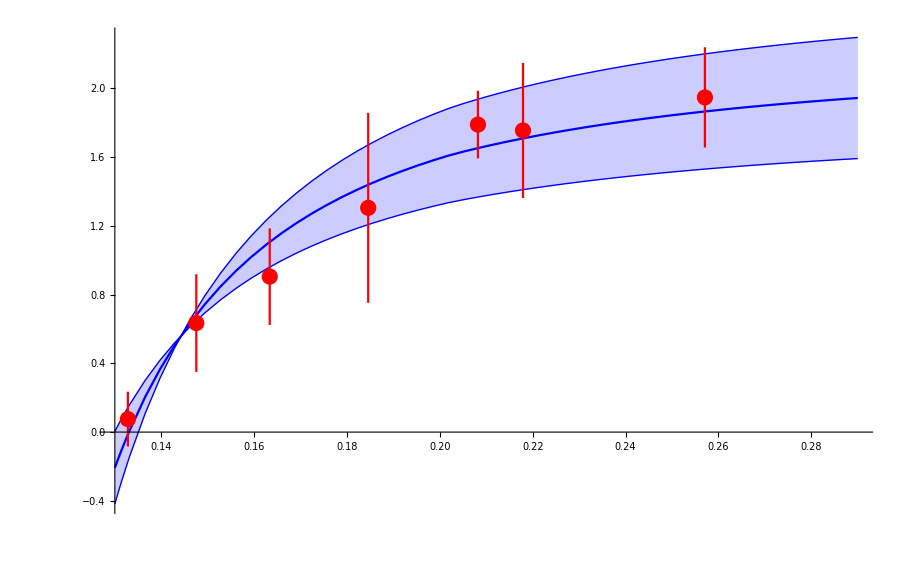

```mathematica
Show[{Plot[{mDcalT[2π,x,k1final[[1]],k2final[[1]]],mDcalT[2π,x,k1final[[1]]+1.96 k1final[[2]],k2final[[1]]-1.96 k2final[[2]]],mDcalT[2π,x,k1final[[1]]-1.96 k1final[[2]],k2final[[1]]+1.96 k2final[[2]]]},{x,0.13,0.29},PlotRange->All,Filling->{1->{2},1->{3}},FillingStyle->Opacity[0.2,Blue],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin}}],ErrorListPlot[Table[{T[[n]](155/172.5),md[[n,1]]/T[[n]] √(σcont[[1]]/σ[[n]]),md[[n,2]]/T[[n]] √(σcont[[1]]/σ[[n]])},{n,1,Length[β]}],PlotRange->All,PlotStyle->{Red}]}]
```

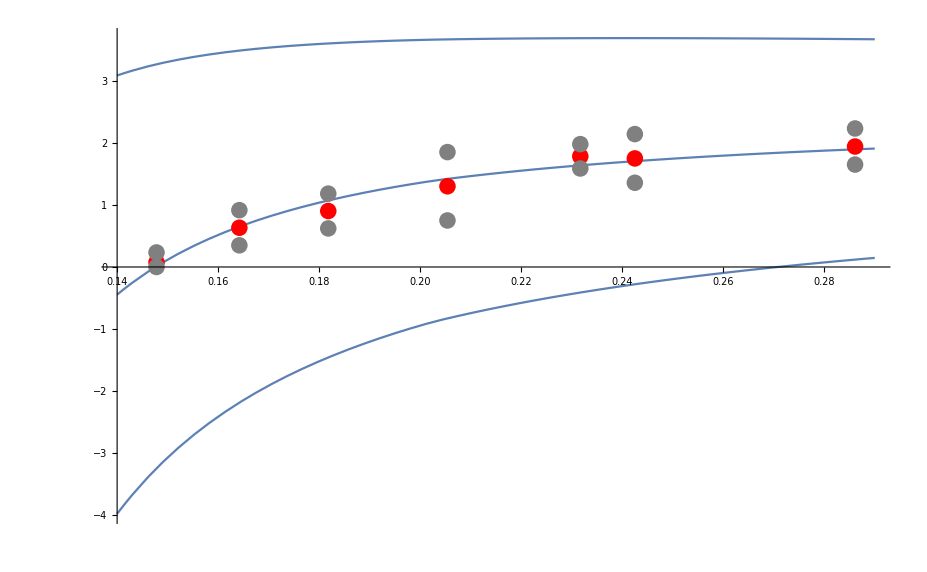

```mathematica
Show[{Plot[mDcalT[2π,x,k1final[[1]],k2final[[1]]],{x,0.14,0.29},PlotRange->All],Plot[mDcalT[2π,x,k1final[[1]]+k1final[[2]],k2final[[1]]+k2final[[2]]],{x,0.14,0.29},PlotRange->All],Plot[mDcalT[2π,x,k1final[[1]]-k1final[[2]],k2final[[1]]-k2final[[2]]],{x,0.14,0.29},PlotRange->All],ListPlot[{Table[{T[[n]],md[[n,1]]/T[[n]] √(σcont[[1]]/σ[[n]])},{n,1,Length[β]}]},PlotRange->All,PlotStyle->{Red}],ListPlot[{Table[{T[[n]],(md[[n,1]]+md[[n,2]])/T[[n]] √(σcont[[1]]/σ[[n]]) },{n,1,Length[β]}]},PlotRange->All,PlotStyle->{Gray}],ListPlot[{Table[{T[[n]],If[md[[n,1]]-md[[n,2]]>0,(md[[n,1]]-md[[n,2]])/T[[n]] √(σcont[[1]]/σ[[n]]) ,0]},{n,1,Length[β]}]},PlotRange->All,PlotStyle->{Gray}]}]
```

## Generate Spectral Functions

```mathematica
R=20000;
Mc=1.4689783072176936;
Mb=4.882;
```

### Define required functions

```mathematica
g[x_]:=Quiet[2NIntegrate[p/(p^2+1)Sinc[p x],{p,0,∞}]];
ϕ[x_]:=Quiet[2NIntegrate[z/((z^2+1)^2)Sinc[x z],{z,0,∞}]];
ReV[r_,m_,α_,σ_,c_]:=-α m-α Exp[-m r]/r-Gamma[1/4]/(2^(3/4)√π)σ/((m^2 σ/α)^(1/4))ParabolicCylinderD[-1/2,√2(m^2 σ/α)^(1/4) r]+Gamma[1/4]/(2Gamma[3/4])σ/((m^2 σ/α)^(1/4))+c
```

```mathematica
Clear[ParabolicCylinderI,ParabolicCylinderR];
ParabolicCylinderI[r_]=If[r<20,ParabolicCylinderD[-1/2,ⅈ √2 r],ⅇ^(r^2/2) (((1-ⅈ) √(1/r))/2^(3/4)+((3/16-(3 ⅈ)/16) (1/r)^(5/2))/2^(3/4)+((105/512-(105 ⅈ)/512) (1/r)^(9/2))/2^(3/4)+((3465/8192-(3465 ⅈ)/8192) (1/r)^(13/2))/2^(3/4)+((675675/524288-(675675 ⅈ)/524288) (1/r)^(17/2))/2^(3/4))];
ParabolicCylinderR[r_]=ParabolicCylinderD[-1/2,√2 r];
```

```mathematica
ϵ=1/1000;ϕ1table=Quiet[ Join[Parallelize[Table[{x,1-ϕ[x]},{x,ϵ/100,2,10ϵ}]],Parallelize[Table[{x,1-ϕ[x]},{x,2+100ϵ,10,100ϵ}]],Parallelize[Table[{x,1-ϕ[x]},{x,10+1000ϵ,100,10000ϵ}]],Parallelize[Table[{x,1-ϕ[x]},{x,100+100000ϵ,10000,100000ϵ}]],Parallelize[Table[{x,1-ϕ[x]},{x,10000+10000000ϵ,1000000,10000000ϵ}]]]];
```

```mathematica
TableT[σ1_,α1_, mD1_]:=Module[{σ=σ1, α=α1,mD=mD1,r,μ,c1},
μ=(mD^2 σ/α)^(1/4);
r=mD/μ;
pg=1;
c1=Re[ParabolicCylinderI[ϵ/100]NIntegrate[ParabolicCylinderR[x] x^2 g[x r],{x,0,∞},PrecisionGoal->pg]];
ψ1[x_,r_]:=c1-ParabolicCylinderR[x]NIntegrate[y^2 g[y r]Re[ParabolicCylinderI[y]],{y,0,x},PrecisionGoal->pg]-Re[ParabolicCylinderI[x]]NIntegrate[ParabolicCylinderR[y] y^2 g[y r],{y,x,∞},PrecisionGoal->pg];
ψ1table=Join[Parallelize[Table[{x,Quiet[ψ1[x,r]]},{x,ϵ/100,1,10ϵ}]],Parallelize[Table[{x,Quiet[ψ1[x,r]]},{x,1+100ϵ,10+ϵ,100ϵ}]],Parallelize[Table[{x,Quiet[ψ1[x,r]]},{x,11,100,1}]],Parallelize[Table[{x,Quiet[ψ1[x,r]]},{x,200,1000,100}]],Parallelize[Table[{x,Quiet[ψ1[x,r]]},{x,2000,20000,1000}]]];];
```

### Modules

```mathematica
swaveccspectra[n_,Tscan_]:=Module[{T=Tscan[[n]],mD=mDcal[2π,Tscan[[n]],k1final[[1]],k2final[[1]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mc,l=0,ρtable,ccsT,Tstring},
TableT[σ,α,mD];

rev=Interpolation[Join[Table[{r,ReV[r,mD,α,σ,c]},{r,0.001,10,0.01}],Table[{r,ReV[r,mD,α,σ,c]},{r,10.1,25,0.1}],Table[{r,ReV[r,mD,α,σ,c]},{r,26,1000,1}],Table[{r,ReV[r,mD,α,σ,c]},{r,1010,20000,10}]]];
ϕ1=Interpolation[ϕ1table,InterpolationOrder->1];
ψ1inter=Interpolation[ψ1table,InterpolationOrder->1];
V[x_]:=rev[x]+ⅈ (α T ϕ1[mD x]+α T ψ1inter[(mD^2 σ/α)^(1/4) x]);

δ=1/100; 
dω=0.0002;ωmin= -1;ωmax=2;
ρtable=Table[{0,0},{x, ωmin, ωmax,dω M}];
SetSharedVariable[ρtable];

ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
(*s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;*)
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2(*+36/(gr1[x])^2*)],rho[δ]==0},rho,{x,δ,inf},PrecisionGoal->10,MaxSteps->1000000];rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ρtable[[it]]={ω+2M,rhow[inf]},{it,1,Length[ρtable]}];

ccsT=Table[{ρtable[[i]][[1]],(-ρtable[[i]][[2]])/(ρtable[[i]][[1]])^2},{i,1,Length[ρtable]}];
Tstring=IntegerPart[T*1000];
Export["spectraldata/Tscan/cc/swccT"<>ToString[Tstring]<>"spectra.dat",ccsT]
]
```

```mathematica
swavebbspectra[n_,Tscan_]:=Module[{T=Tscan[[n]],mD=mDcal[2π,Tscan[[n]],k1final[[1]],k2final[[1]]],σ=σcont,α=αcont,c=ccont,M=Mb,l=0,ρtable,bbsT,Tstring},
TableT[σ,α,mD];

rev=Interpolation[Join[Table[{r,ReV[r,mD,α,σ,c]},{r,0.001,10,0.01}],Table[{r,ReV[r,mD,α,σ,c]},{r,10.1,25,0.1}],Table[{r,ReV[r,mD,α,σ,c]},{r,26,1000,1}],Table[{r,ReV[r,mD,α,σ,c]},{r,1010,20000,10}]]];
ϕ1=Interpolation[ϕ1table,InterpolationOrder->1];
ψ1inter=Interpolation[ψ1table,InterpolationOrder->1];
V[x_]:=rev[x]+ⅈ (α T ϕ1[mD x]+α T ψ1inter[(mD^2 σ/α)^(1/4) x]);

δ=1/100; 
dω=0.0002;ωmin= -1;ωmax=3;
ρtable=Table[{0,0},{x, ωmin, ωmax,dω M}];
SetSharedVariable[ρtable];

ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
(*s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;*)
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2(*+36/(gr1[x])^2*)],rho[δ]==0},rho,{x,δ,inf},PrecisionGoal->10,MaxSteps->1000000];rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ρtable[[it]]={ω+2M,rhow[inf]},{it,1,Length[ρtable]}];

bbsT=Table[{ρtable[[i]][[1]],ρtable[[i]][[2]]},{i,1,Length[ρtable]}];

Tstring=IntegerPart[T*1000];
Export["spectraldata/Tscan/bb/swbbT"<>ToString[Tstring]<>"spectra.dat",bbsT]
]
```

### Run modules

```mathematica
Off[NIntegrate::inumr]
```

```mathematica
Tscanorig=Table[i,{i,0.15,0.25,0.003}];
Tscanc=Table[i,{i,0.174,0.25,0.003}];
Do[swaveccspectra[i,Tscanc],{i,Length[Tscanc]}]//AbsoluteTiming
```

$Aborted

```mathematica
Tscanb=Table[i,{i,0.15,0.6,0.005}];
Do[swavebbspectra[i,Tscanb],{i,Length[Tscanb]}]//AbsoluteTiming
```